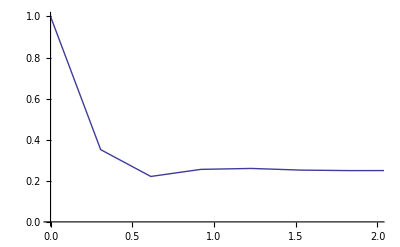

```mathematica
Omega=1.46446*163*2*Pi*1000;
Gama= 5.6*2*Pi*1000;
X = 0.0001;
delta = 914.0*2*Pi;
Delta = -12.0*2*Pi*1000000;
phi=0.55Degree;
fr=Omega^2/(Gama^2+4*Delta^2);

a= fr*Gama;
b=fr*Gama+X;
c=delta;
d=fr*Delta;  
e=phi;

Plot[{0.25*(1+Exp[-(a*x)]+2*Exp[-(0.5*(a+b)*x)]*Cos[(c+d)*x+e]) }, {x,0,1000},PlotRange->{{0,2},{0,1}}]
```